## Creating Fitting Functions for Binary Love Relations

In this script, I create the fitting functions for the λs-λa and Λ-δΛ relations. Somehow, the fitting coefficients are different from those presented in the paper. I’ll compare the fit here with that in the paper to show that the difference is very small.

```mathematica
list["NS"]={"eos1","eos2","eos3","eos4","eos5","eos6","eos7","eos8","eos9","eos10","eos11","eos12","eos13","eos14","eos15","eos16","eos17","eos18","eos19","eos20","eos21","eos22","eos23","eos24","eos25","eos26","eos27","eos28","eos29","eos30","eos31","eos32","eos33","eos34","eos35"};
```

### λs-λa

#### Loading Data

Meaning of each column in the data file
1: mass ratio
2: λs
3: λa

```mathematica
(dataforfitλsλa[#]=Import[NotebookDirectory[]<>"unconstrained/"<>ToString[#]<>".dat"])&/@list["NS"];
```

#### Fitting Functions

Combining Data

```mathematica
dataforfitNSλsλaAll=Flatten[Union[(dataforfitλsλa[#])&/@list["NS"]],1];
```

Newtonian relation
q: mass ratio, n: polytropic index

```mathematica
dataforfitNSλsλa=Drop[dataforfitNSλsλaAll,0,{4,-1}]
```

{{0.936227,265.335,57.4023},{0.697476,248.55,229.459},{0.835095,84.7322,62.5301},17644,{0.865321,948.184,345.018},{0.839223,227.774,116.816},{0.821755,267.756,147.483}}
 |  |  |  |

```mathematica
λsλaNewtonq[q_,n_]=(1-q^(10/(3-n)))/(1+q^(10/(3-n)));
```

Fitting Function
x: mass ratio, y: λbar_s

```mathematica
fitλsλaFunction=λsλaNewtonq[x,n] y(1+(b11 x+b12 x^2) y^(-1/5)+ (b21 x+b22 x^2) y^(-2/5)+ (b31 x+b32 x^2) y^(-3/5))/(1+(c11 x+c12 x^2) y^(-1/5)+ (c21 x+c22 x^2) y^(-2/5)+ (c31 x+c32 x^2) y^(-3/5))
```

((1-x^(10/(3-n))) (1+(b31 x+b32 x^2)/y^(3/5)+(b21 x+b22 x^2)/y^(2/5)+(b11 x+b12 x^2)/y^(1/5)) y)/((1+x^(10/(3-n))) (1+(c31 x+c32 x^2)/y^(3/5)+(c21 x+c22 x^2)/y^(2/5)+(c11 x+c12 x^2)/y^(1/5)))

For convenience this is the parameter list

```mathematica
params={b11,b12,b21,b22,b31,b32,c11,c12,c21,c22,c31,c32};
```

```mathematica
paramsStart={{b11,-0.54},{b12,3.93},{b21,-47.55},{b22,61.77},{b31,77.65},{b32,-111.56},{c11,-6.41},{c12,11.48},{c21,-4.19},{c22,-4.06},{c31,15.13},{c32,-18.25}};
```

This makes the fitted model, with lots of internal information

```mathematica
fitλsλa=NonlinearModelFit[dataforfitNSλsλa,fitλsλaFunction/.{n->0.743},paramsStart,{x,y},MaxIterations->1000]
```

NonlinearModelFit[{{0.936227,265.335,57.4023},{0.697476,248.55,229.459},{0.835095,84.7322,62.5301},17645,{0.839223,227.774,116.816},{0.821755,267.756,147.483}},3,MaxIterations→1000]
 |  |  |  |

```mathematica
fitλsλa["ParameterTable"]
```

NonlinearModelFit[{{0.936227,265.335,57.4023},{0.697476,248.55,229.459},{0.835095,84.7322,62.5301},17645,{0.839223,227.774,116.816},{0.821755,267.756,147.483}},3,MaxIterations→1000][ParameterTable]
 |  |  |  |

```mathematica
bestfitparams=params/.fitλsλa["BestFitParameters"];
```

```mathematica
Cov=fitλsλa["CovarianceMatrix"];
```

#### Examining residuals

```mathematica
residualvals=fitλsλa["FitResiduals"];
```

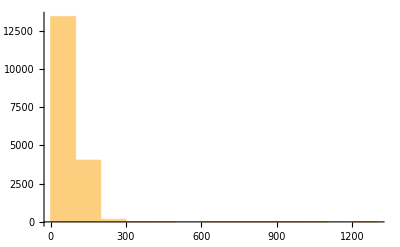

```mathematica
Histogram[residualvals]
```

We also want the scaled residuals; for this I’m assuming that the ordering of the residuals is the same as the data points:

```mathematica
lambdaAall=dataforfitNSλsλa[[;;,3]];
```

```mathematica
scaledresidualvals = residualvals/lambdaAall;
```

```mathematica
StandardDeviation[scaledresidualvals]
```

0.139061

```mathematica
Mean[scaledresidualvals]
```

0.209876

This doesn’t plot well

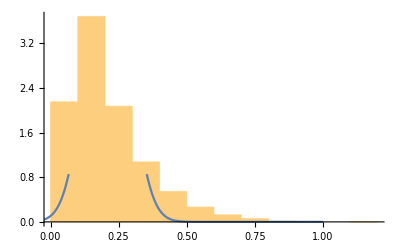

```mathematica
Show[Histogram[scaledresidualvals,Automatic,"PDF"],Plot[PDF[NormalDistribution[Mean[scaledresidualvals],0.075],x],{x,-1,1}]]
```

Now look at the structure of the (unscaled) residuals

```mathematica
resVsq = {dataforfitNSλsλa[[;;,1]],residualvals}//Transpose;
```

```mathematica
resVsLs = {dataforfitNSλsλa[[;;,2]],residualvals}//Transpose;
```

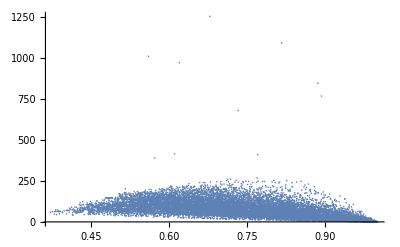

```mathematica
ListPlot[resVsq,PlotRange->All]
```

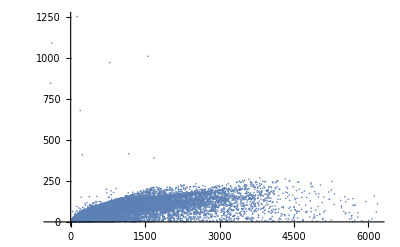

```mathematica
ListPlot[resVsLs,PlotRange->All]
```

```mathematica
scaledresVsq = {dataforfitNSλsλa[[;;,1]],scaledresidualvals}//Transpose;
```

```mathematica
scaledresVsLs = {dataforfitNSλsλa[[;;,2]],scaledresidualvals}//Transpose;
```

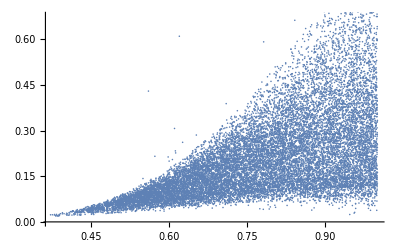

```mathematica
ListPlot[scaledresVsq]
```

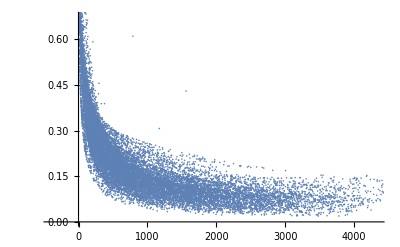

```mathematica
ListPlot[scaledresVsLs]
```

#### Export residuals

I’ll export the residuals and scaled residuals as a table of tuples (q,λs,λa)

```mathematica
residualtab={dataforfitNSλsλa[[;;,1]],dataforfitNSλsλa[[;;,2]],dataforfitNSλsλa[[;;,3]],residualvals,scaledresidualvals}//Transpose;
```

```mathematica
residualtab[[1;;2]]
```

{{0.936227,265.335,57.4023,18.9403,0.329957},{0.697476,248.55,229.459,64.669,0.281833}}

```mathematica
Export[NotebookDirectory[]<>"UniversalRelationsResidualsUnConstrained.dat",residualtab]
```

/Users/rina/research/projects/UR-recalibration/data/UniversalRelationsResidualsUnConstrained.dat

### Making some test samples from the fit covariance matrix

```mathematica
dist=MultinormalDistribution[bestfitparams,Cov];
```

Uncomment this and run if something has changed above. This will generate new samples.

```mathematica
(*GaussSamps=RandomVariate[dist,10^4];*)
```

Instead, import the samples:

```mathematica
GaussSamps = Import[NotebookDirectory[]<>"ToySamples.dat"];
```

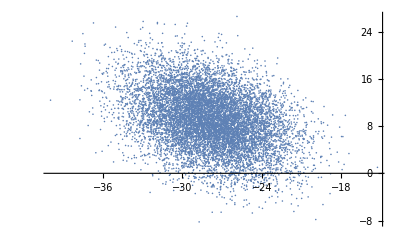

```mathematica
ListPlot[{GaussSamps[[;;,1]],GaussSamps[[;;,2]]}//Transpose]
```

```mathematica
(*Export[NotebookDirectory[]<>"ToySamples.dat",GaussSamps]*)
```

/Users/aaron/GitRepos/WeLoveBinaryLove/Mathematica/ToySamples.dat

### Comparing test samples to tabulated EoS (the actual data)

```mathematica
fitλsλaFunction/.{x->q,y->Ls}
```

(Ls (1-q^(10/(3-n))) (1+(b11 q+b12 q^2)/Ls^(1/5)+(b21 q+b22 q^2)/Ls^(2/5)+(b31 q+b32 q^2)/Ls^(3/5)))/((1+q^(10/(3-n))) (1+(c11 q+c12 q^2)/Ls^(1/5)+(c21 q+c22 q^2)/Ls^(2/5)+(c31 q+c32 q^2)/Ls^(3/5)))

```mathematica
lambdaAfunc[q_,Ls_,b11_,b12_,b21_,b22_,b31_,b32_,c11_,c12_,c21_,c22_,c31_,c32_,n_:0.743]:=(Ls (1-q^(10/(3-n))) (1+(b11 q+b12 q^2)/Ls^(1/5)+(b21 q+b22 q^2)/Ls^(2/5)+(b31 q+b32 q^2)/Ls^(3/5)))/((1+q^(10/(3-n))) (1+(c11 q+c12 q^2)/Ls^(1/5)+(c21 q+c22 q^2)/Ls^(2/5)+(c31 q+c32 q^2)/Ls^(3/5)))
```

```mathematica
lambdaAfunc//Apply[#,Join[dataforfitNSλsλa[[1,1;;2]],GaussSamps[[1]]]]&
```

938.629

```mathematica
appliedsamps=Table[lambdaAfunc//Apply[#,Join[dataforfitNSλsλa[[100,1;;2]],GaussSamps[[i1]]]]&,{i1,Length[GaussSamps]}];
```

The histogram appears to be way off:

```mathematica
dataforfitNSλsλa[[100,3]]
```

1489.29

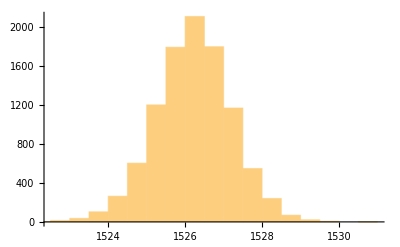

```mathematica
Histogram[appliedsamps]
```

#### Comparison with the fitting parameters in the paper

b1 means b11, b2 means b12, c1 means b21, etc. 
They are in the same order as above.

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0755014 | 0.0224842 | 3.35798 | 0.000790901
b1 | -2.23521 | 0.44714 | -4.99891 | 5.95847×10^-7
b2 | 0.84736 | 0.323204 | 2.62175 | 0.0087739
c1 | 10.4508 | 1.14704 | 9.11108 | 1.14832×10^-19
c2 | -3.25082 | 1.91777 | -1.6951 | 0.090117
cc1 | -15.7042 | 0.584605 | -26.863 | 8.70314×10^-149
cc2 | 13.6101 | 0.579853 | 23.4716 | 8.93932×10^-116
d1 | -2.04761 | 0.400315 | -5.11499 | 3.25247×10^-7
d2 | 0.59756 | 0.391955 | 1.52456 | 0.127431
e1 | 7.94119 | 0.624877 | 12.7084 | 1.88594×10^-36
e2 | 0.5658 | 3.59058 | 0.157579 | 0.874795
ee1 | -7.3595 | 2.92446 | -2.51653 | 0.0118821
ee2 | -1.32001 | 6.62585 | -0.199221 | 0.842098

```mathematica
afitλsλaPaper=0.07550142319214329;
b11fitλsλaPaper=-2.235211564600799;
b12fitλsλaPaper=0.8473602651452113;
b21fitλsλaPaper=10.450768890658436;
b22fitλsλaPaper=-3.2508175069052236;
b31fitλsλaPaper=-15.70422718116218;
b32fitλsλaPaper=13.610086144200915;
c11fitλsλaPaper=-2.0476075062457624;
c12fitλsλaPaper=0.5975598353307647;
c21fitλsλaPaper=7.941186603745042;
c22fitλsλaPaper=0.5657997369005573;
c31fitλsλaPaper=-7.359501034119938;
c32fitλsλaPaper=-1.3200089940337225;
```

```mathematica
fitλsλaFunctionYY=λsλaNewtonq[x,n] y(a+(b11 x+b12 x^2) y^(-1/5)+ (b21 x+b22 x^2) y^(-2/5)+ (b31 x+b32 x^2) y^(-3/5))/(a+(c11 x+c12 x^2) y^(-1/5)+ (c21 x+c22 x^2) y^(-2/5)+ (c31 x+c32 x^2) y^(-3/5))
```

((1-x^(10/(3-n))) (a+(b31 x+b32 x^2)/y^(3/5)+(b21 x+b22 x^2)/y^(2/5)+(b11 x+b12 x^2)/y^(1/5)) y)/((1+x^(10/(3-n))) (a+(c31 x+c32 x^2)/y^(3/5)+(c21 x+c22 x^2)/y^(2/5)+(c11 x+c12 x^2)/y^(1/5)))

```mathematica
fitλsλaPaper[x_,y_]=fitλsλaFunctionYY/.{n->0.743,a->afitλsλaPaper,b11->b11fitλsλaPaper,b12->b12fitλsλaPaper,b21->b21fitλsλaPaper,b22->b22fitλsλaPaper,b31->b31fitλsλaPaper,b32->b32fitλsλaPaper,c11->c11fitλsλaPaper,c12->c12fitλsλaPaper,c21->c21fitλsλaPaper,c22->c22fitλsλaPaper,c31->c31fitλsλaPaper,c32->c32fitλsλaPaper};
```

```mathematica
fitλsλa[0.9,100]
fitλsλaPaper[0.9,100]
```

22.926

38.2844

```mathematica
Length[testdata]
```

532

```mathematica
?Append
```

Append[expr,elem] gives expr with elem appended. 
Append[elem] represents an operator form of Append that can be applied to an expression.

```mathematica
For[SlyVals={};i1=1,i1≤Length[dataforfitNSλsλa],i1++,
If[Abs[0.9-dataforfitNSλsλa[[i1,1]]]≤0.01,SlyVals=Append[SlyVals,dataforfitNSλsλa[[i1]] ],Null
];
];
```

```mathematica
SlyVals
```

{{0.896447,306.885,109.593,232.901},{0.900658,93.0829,40.1261,73.2241},{0.905178,896.619,255.719,656.281},{0.900967,90.9719,39.4376,71.6465},{0.907193,1579.37,408.556,1140.32},{0.908803,121.945,44.5083,92.9059},{0.896703,585.372,192.326,437.98},{0.897848,1576.69,449.524,1154.},{0.902624,1411.83,389.229,1028.36},{0.895647,135.027,55.0688,105.043},{0.899483,215.175,78.1581,163.793},{0.906932,292.238,94.5179,218.093},{0.895806,67.9364,38.8685,57.0359},{0.898726,223.392,81.3235,170.116},{0.891098,290.687,109.801,222.854},{0.89279,2558.73,720.251,1869.3},{0.906919,646.535,189.015,474.965},{0.907372,1138.49,307.144,826.733},{0.905485,202.93,69.9536,153.064},{0.895086,1247.5,376.831,920.996},{0.904234,245.941,83.6562,185.084},{0.898097,395.345,134.661,297.589},{0.904658,236.304,80.4552,177.861},{0.909545,3719.84,842.861,2640.97},{0.909452,214.798,70.4003,160.649},{0.905121,236.03,79.9888,177.515},{0.893476,234.942,89.2617,180.312},{0.907541,144.429,51.5361,109.594}}

```mathematica
?Interpolation
```

RowBox[{"Interpolation", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] constructs an interpolation of the function values SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]], assumed to correspond to StyleBox["x", "TI"] values 1, 2, … . 
RowBox[{"Interpolation", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] constructs an interpolation of the function values SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]] corresponding to StyleBox["x", "TI"] values SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]].
RowBox[{"Interpolation", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] constructs an interpolation of multidimensional data.
RowBox[{"Interpolation", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["df", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] constructs an interpolation that reproduces derivatives as well as function values.
RowBox[{"Interpolation", "[", RowBox[{StyleBox["data", "TI"], ",", StyleBox["x", "TI"]}], "]"}] find an interpolation of StyleBox["data", "TI"] at the point StyleBox["x", "TI"].

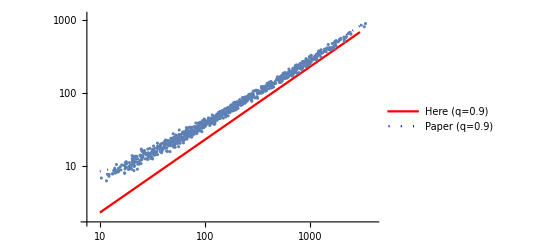

```mathematica
Show[LogLogPlot[{fitλsλa[0.9,x],fitλsλaPaper[0.9,x]},{x,10,3000},PlotLegends->{"Here (q=0.9)","Paper (q=0.9)"},FrameLabel->{"λs","λa"},PlotStyle->{Red,{Blue,Dotted}}],ListLogLogPlot[{SlyVals[[;;,2]],SlyVals[[;;,3]]}//Transpose]]
```

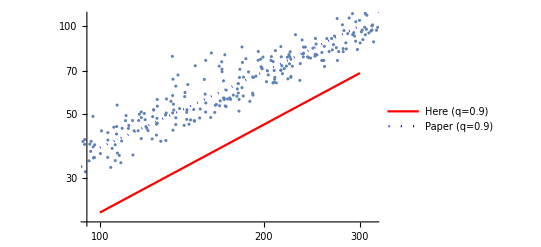

```mathematica
Show[LogLogPlot[{fitλsλa[0.9,x],fitλsλaPaper[0.9,x]},{x,100,300},PlotLegends->{"Here (q=0.9)","Paper (q=0.9)"},FrameLabel->{"λs","λa"},PlotStyle->{Red,{Blue,Dotted}}],ListLogLogPlot[{SlyVals[[;;,2]],SlyVals[[;;,3]]}//Transpose]]
```

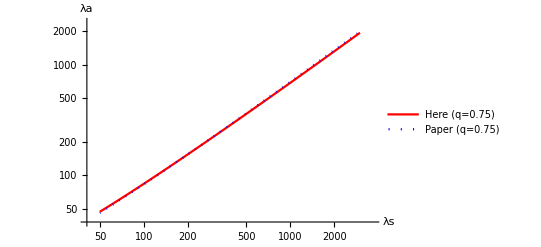

```mathematica
LogLogPlot[{fitλsλa[0.75,x],fitλsλaPaper[0.75,x]},{x,50,3000},PlotLegends->{"Here (q=0.75)","Paper (q=0.75)"},AxesLabel->{"λs","λa"},PlotStyle->{Red,{Blue,Dotted}}]
```